```mathematica
Get[StringJoin[NotebookDirectory[],"PlaneCurvePlot.wl"]]
```

## Parallel

#### (* Sinusoid and its parallel *)

```mathematica
PlaneCurvePlot[{t,Sin[t]},{t,0,3 π,.1},ParallelCurveOffset->{3},NormalLineLength->6,PlotDot->False,NormalLineStyle->{Hue[.17]},AspectRatio->Automatic,PlotRange->{{-2.5,11.5},{-2,4}}]
```

-Graphics-

#### (* Lemniscate of Bernoulli and its parallel *)

```mathematica
PlaneCurvePlot[{Cos[t]/(1+Sin[t]^2),(Sin[t] Cos[t])/(1+Sin[t]^2)},{t,0,2 π,.07},ParallelCurveOffset->{.175,.35,.7},PlotDot->False,DotStyle->{Hue[.9],Hue[.7],Hue[0]},AspectRatio->Automatic,PlotRange->All]
```

-Graphics-

#### (*3 leaved rose and its parallel *)

```mathematica
PlaneCurvePlot[{Cos[3 t] Cos[t],Cos[3 t] Sin[t]},{t,0,π,.015},ParallelCurveOffset->{.18,.4,.6},PlotDot->False,DotStyle->{Hue[0],Hue[.3],Hue[.7]},AspectRatio->Automatic,PlotRange->All]
```

-Graphics-

#### (* Astroid and its parallel *)

```mathematica
PlaneCurvePlot[{(3 Cos[t])/4+1/4 Cos[3 t],(3 Sin[t])/4-1/4 Sin[3 t]},{t,0,2 π,(2 π)/160},ParallelCurveOffset->{.3,.5,1},PlotDot->False,CurveStyle->{Thickness[.007]},DotStyle->{Hue[.6],Hue[.8],Hue[0]},AspectRatio->Automatic,Axes->False]
```

-Graphics-

#### (* Hypotrochoid parallel beauty, [1,1/5,.13] *)

```mathematica
PlaneCurvePlot[{(4 Cos[t])/5+0.13 Cos[4 t],(4 Sin[t])/5-0.13 Sin[4 t]},{t,0,2 π,(2 π)/(5 30)},ParallelCurveOffset->Table[i,{i,-.5,.5,.1}],Axes->False,PlotDot->False,DotStyle->Table[Hue[Random[]],{20}],AspectRatio->Automatic]
```

-Graphics-

#### (* Hypotrochoid parallel beauty. Rotate[Hypocycloid[3][t], Pi/2] *)

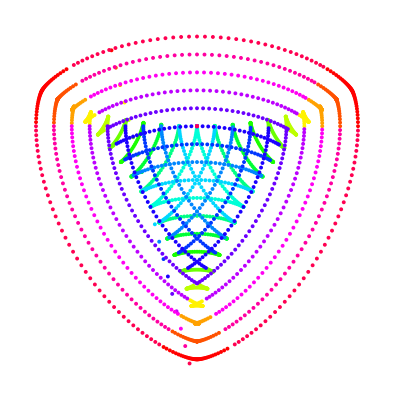

```mathematica
Clear[myOffset,myStyle];
myOffset=Table[i,{i,-3,3,6/18}];
myStyle=Table[{Hue[i],PointSize[.007]},{i,0,1,1/Length[myOffset]}];
PlaneCurvePlot[{-(2 Sin[t])/3+1/3 Sin[2 t],(2 Cos[t])/3+1/3 Cos[2 t]},{t,0,2 π,(2 π)/(3 40)},ParallelCurveOffset->myOffset,PlotDot->False,PlotCurve->False,DotStyle->myStyle,LineStyle->{GrayLevel[0]},Axes->False,AspectRatio->Automatic]
Clear[myOffset,myStyle];
```